Musical Rule Characterization & Composition

Dobbs, Michael

Roy, Xavier

Sonoma State University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: 
Create the rule-space of L-scale notes with n neighbouring notes and observe the patterns and distributions created after a number of iterations on the space of initializations.

Additionally, create a list of enumerated primitives that act on musical notes and observe the structure and patterns that emerge when they are applied successively. This list will cover elementary actions such as inversion, retrograde, diminution, and scale shifting. Furthermore, these rules will be applied randomly to create a musical composition.

SUMMARY OF WORK: 
The note rule-space was fabricated and enumerated for n neighbouring notes. A histogram of time spent on a note throughout the iteration was created for arbitrary rules in the space.

Additionally, the list of primitives described in the “Goal” section was created and random compositions were made. Some variables implemented include the number of notes, tempo, type of instrument(s), and relative volume between the instruments.

RESULTS AND FUTURE  WORK:
The 12-note rule-space converges to a cyclic group of maximum length L in a maximum number of time-steps of L. While the algorithmic composer exhibits musical structure, it is not guaranteed to be aesthetically pleasing.
	
Generalize the rule for scales of length L, consider chords, and implement a probabilistic rule. Additionally, implement chord progression and drums in the algorithmic composer.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

L-Note Rulespace

## 1-Note Neighbourhood, Pentatonic Scale:

## 1-Note Neighbourhood, Chromatic Scale:

## 2-Note Neighbourhood, Chromatic Scale:

Algorithmic Composer

Shamisen,Shamisen, 100bmp, on {0, 4, 7}, for 30+s.

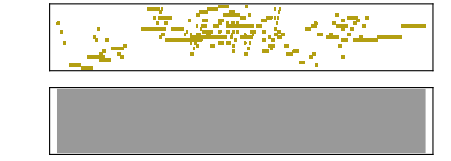

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

For the musical rule characterization, a function was created that generates the path a set of notes will take given a specific rule number. A general L-note scale was used to implement this function. The function considers the past n-notes as neighbors and generates an enumerated ruleset which one may choose from to create the pattern. First, the rules must be enumerated based on the number of neighbors, n: there exist L different outputs for each of the rules, each with n neighbors that have L different outputs as well; thus the total number of rules is L^(L^n). Next, a function was created to append the new note to the list based on the previous n neighbours. This function was then nested to be able to apply the function to the initial conditions m times. Then for a given rule, a function was created to apply the rule to all of the possible initial conditions with n neighbours m times. These sets are then plotted with a ListLinePlot and the distribution of the amount of time spent on a single note is visualized with a Histogram.

For the algorithmic composition of music, a palette of primitives was created to be applied to a set of basis notes (in my case, an L-note scale measured by pitch classes with middle C = 0). The list of primitives includes transpose, retrograde, inversion, scale-shifting, diminution, and compositions of these. Transpose takes the motive (a list of ordered and spaced pitch classes available for the user to specify) and transforms them into all L starting notes. This function shows up in all other primitives as a way of creating a list of notes to randomize the output when compiled. Inversion inverts each individual relationship between the notes (i.e. AB → AG, etc.). ScaleShift maps the given notes a semitone higher on the scale. Retrograde reverses the note order (i.e. {0,4,7} → {7, 4, 0}). Diminution divides a set of long notes into a series of shorter notes (i.e. {0,2,4} →{0,1,2,3,4}). These functions, along with their compositions, are then compiled into a palette to be used randomly to create music. The function DurationalL randomly chooses the duration of each note from a given distribution. The Variation function turns each set of pitch classes that have passed through a random function in the palette into a sound of a given instrument. These variations are then sent to the Voice functions which randomly choose to play notes or rest at each time step, then append the notes together into one output. The compiler combines both voices together into one sound object. This object is then sent to the user interface, where one may specify the instrument to the play the notes, the relative sound between the two instruments, the pitch class to be used, the tempo, and length of the song.

Code

Provide one of:

Link to the GitHub

```mathematica
Hyperlink["DobbsWSS17Project","https://github.com/dobbsm/WSS17/blob/master/AlgComposer.nb"]
```

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

The 12-note rule-space converges to a cyclic group of maximum length 12 in a maximum number of time-steps of 12. The distributions that emerge are uniform for notes that share the same number of occurrences in the rule. The relative heights of these distributions are proportional to the number of notes that are mapped to the cycle and the length of the cycle.

While the algorithmic composer exhibits musical structure, it is not guaranteed to be aesthetically pleasing. Chords are implemented, however they sound pleasing only if the pitch class is initialized by the user in such a way as to create a recognizable major or minor chord. For the time being, there is no inherent structure in the relationship between the two instruments (other than a different ratio of playing to resting).

All Visualizations

Note progression and note density of histogram of rule 891610044825 for 1 neighbour.

Note progression and note density of histogram of rule 2.52×10^155 for 2 neighbours.

The Algorithmic Composer user interface.

An example of the output of such an interface.

Piano,Violin, 100bmp, on {0, 4, 7}, for 30+s.

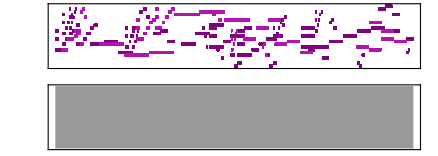

Data Sources Links/References

Future Directions

Future work on the rule project includes generalizing the rule for scales of length L and considering chords. 

Future work on the algorithmic composer project includes implementing chord progression, adding a percussion section to the symphony, and creating structure between the two instruments (such as solos, concurrently playing bass and lead, etc.). I would also like to learn about music theory so as to approach this project with a more appropriate background.

Background Info Links/References

Rule-based programming background and inspiration:

```mathematica
Hyperlink["Cellular Automaton; Wolfram MathWorld","http://mathworld.wolfram.com/CellularAutomaton.html"]
```

Music theory background:

```mathematica
Hyperlink["Music Theory","https://www.musictheory.net/"]
```

Keywords

Provide keywords as items

Music

Music Patterns

Music Rules

Music Primitives

Music Generation

Musical Composition

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```